Вариант 7 Логаш Полина

1.1  Пусть функция f(x)∈MC^(n+1), задана на отрезке [-1,1] аналитически. Построить интерполяционный многочлен P(x) ≈f(x) указанной
степени n с минимальной верхней гранью погрешности по оптимальным узлам  x_k=Cos[(π(2k+1))/(2(n+1))], k=0,...,n.

```mathematica
f[x_]=5^x;
n=4;
a =-1; b=1;
Do[{Subscript[x, k]=Cos[(π(2k+1))/(2(n+1))], Subscript[f, k]=f[Subscript[x, k]]},{k,0,n}]
L[x_]=∑_(k=0)^n (∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))Subscript[f, k]//Expand//N
```

1.+1.57907 x+1.28715 x^2+0.814482 x^3+0.311174 x^4

1.2 Оценить погрешность интерполирования

```mathematica
M1=Maximize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M2=Minimize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M=Max[Abs[M1],Abs[M2]];
R=M/((n+1)!2^n)//N
```

0.0281216

1.3 Изобразить исходную функцию, узлы и полученный интерполяционный многочлен в одной системе координат

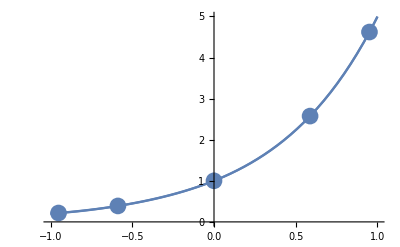

```mathematica
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr1=Plot[f[x],{x,a,b}];
Gr2=Plot[L[x],{x,a,b}];
Gr3=ListPlot[Tbl,PlotStyle->{PointSize[0.03]}];
Show[Gr1,Gr2,Gr3]
```

2.1 Построить интерполяционный многочлен  с минимальной верхней гранью погрешности, не превышающей ε. Определить из условия оценки верхней грани погрешности.

```mathematica
f[x_]=Cos[2x];
a=0;
b=4;
ε=10^-5;
M1:=Maximize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M2:=Minimize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M:=Max[Abs[M1],Abs[M2]];
n=1;
While[(R=(M(b-a)^(n+1))/((n+1)!2^n))>ε,n++]
n
R<ε
Do[{Subscript[x, k]=(b-a)/2 Cos[(π(2k+1))/(2(n+1))]+(a+b)/2,Subscript[f, k]=f[Subscript[x, k]]},{k,0,n}]
L[x_]=L[x_]=∑_(k=0)^n (∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))Subscript[f, k]//Expand//N
```

18

True

1.-2.95404×10^-9 x-2. x^2+1.45985×10^-7 x^3+0.666665 x^4+6.45593×10^-6 x^5-0.0889047 x^6+0.0000276952 x^7+0.00631414 x^8+0.0000324631 x^9-0.000304754 x^10+0.0000117147 x^11+4.0175×10^-6 x^12+1.26783×10^-6 x^13-4.27301×10^-7 x^14+2.41793×10^-8 x^15+3.80588×10^-9 x^16-5.65078×10^-10 x^17+2.18909×10^-11 x^18

2.2 Изобразить исходную функцию, узлы и полученный интерполяционный многочлен в одной системе координат.

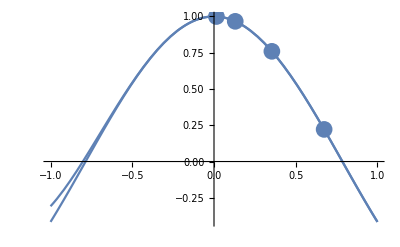

```mathematica
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr1=Plot[f[x],{x,Min[X],Max[X]}];
Gr2=Plot[L[x],{x,Min[X],Max[X]}];
Gr3=ListPlot[Tbl,PlotStyle->{PointSize[0.03]}];
Show[Gr1,Gr2,Gr3]
```